```mathematica
DSolve[a''[t]*a[t]+(a'[t])^2-(a[t])^(-1/2)==0, a[t], t]
```

{{a[t]→InverseFunction[-((√3 (3 C[1]+4 #1^(3/2))-3 C[1] Hypergeometric2F1[1/3,1/2,4/3,-(4 #1^(3/2))/(3 C[1])] √(3+(4 #1^(3/2))/C[1]))/(5 √#1 √((3 C[1]+4 #1^(3/2))/#1^2)))&][t+C[2]]},{a[t]→InverseFunction[(√3 (3 C[1]+4 #1^(3/2))-3 C[1] Hypergeometric2F1[1/3,1/2,4/3,-(4 #1^(3/2))/(3 C[1])] √(3+(4 #1^(3/2))/C[1]))/(5 √#1 √((3 C[1]+4 #1^(3/2))/#1^2))&][t+C[2]]}}

```mathematica
c := 3*10^(10) 
G:= 6.67*10^(-8)
ρ0 :=  1.84*10^(-8) (* este es el valor que usamos en la tesis*)o
ati := 2.5*10^(-9)
n := 1/2
```

```mathematica
k = (4π *G)/(3*c^2)*ρ0 *(ati)^(3-n)
```

1.78501×10^-57

```mathematica
ti := 0.74 (*s*)
Hti := 0.67 (* 1/s*)
Dati := Hti * ati (* 1/s*)
```

```mathematica
τi = √k*ti
Daτi = 1/(√k)*Dati
```

3.12645×10^-29

3.96456×10^19

```mathematica
NDSolve[{a''[t]*a[t]+(a'[t])^2 -(a[t])^(-1/2)==0, a[τi]== ati, a'[τi] == Daτi}, a[t], {t, τi, √k*10^4}]
```

{{a[t]→InterpolatingFunction[…][t]}}

```mathematica
√k*10^4
```

4.22493×10^-25

```mathematica
sol=%
a05[τ_]:=a[τ]/. sol[[1]]
```

{{a[t]→InterpolatingFunction[…][t]}}

```mathematica
aRadτ[t_] := ar*(√k t)^(1/2)
```

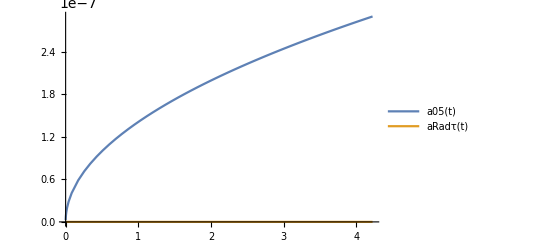

```mathematica
Plot[{a05[t],aRadτ[t]},{t,3.126450873821958*^-29,4.224933613272917*^-25},PlotRange->All, PlotLegends->"Expressions"]
```

```mathematica
DSolve[a''[t]*a[t]+(a'[t])^2-1==0, a[t], t]
```

{{a[t]→-√(-ⅇ^(2 C[1])+t^2+2 t C[2]+C[2]^2)},{a[t]→√(-ⅇ^(2 C[1])+t^2+2 t C[2]+C[2]^2)}}

```mathematica
a1AB[τ_]:= √(-E[2*A]+τ^2+2B τ+B^2)
```

```mathematica
D[a1[t], t]
```

(2 B+2 t)/(2 √(B^2+2 B t+t^2-ⅇ[2 A]))

```mathematica
NSolve[{ati^2== τi^2+2B τi+C,  Daτi=(B+τi)/(√(C+τi^2+2B τi))}, {C,B}]
```

```mathematica
{{C->6.250000000000001*^-18,B->0.}}
```

```mathematica
B := 0
```

```mathematica
A:= 6.250000000000001*^-18
```

```mathematica
a1BC[τ_]:=√(A+τ^2+2B τ)
```

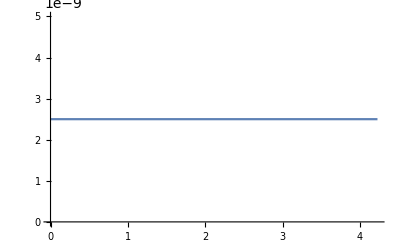

```mathematica
Plot[a1BC[τ], {τ, τi, √k*10^4}]
```

```mathematica
DSolve[a''[t]*a[t]+(a'[t])^2-(a[t])==0, a[t], t]
```

{{a[t]→InverseFunction[-(Hypergeometric2F1[1/2,2/3,5/3,-(2 #1^3)/(3 C[1])] #1^2 √(1+(2 #1^3)/(3 C[1])))/(2 √(C[1]+(2 #1^3)/3))&][t+C[2]]},{a[t]→InverseFunction[(Hypergeometric2F1[1/2,2/3,5/3,-(2 #1^3)/(3 C[1])] #1^2 √(1+(2 #1^3)/(3 C[1])))/(2 √(C[1]+(2 #1^3)/3))&][t+C[2]]}}

```mathematica
n :=2
k = (4π *G)/(3*c^2)*ρ0 *(ati)^(3-n)
```

1.42801×10^-44

```mathematica
τi = √k*ti
Daτi = 1/(√k)*Dati
```

8.84294×10^-23

1.40168×10^13

```mathematica
NDSolve[{a''[t]*a[t]+(a'[t])^2 -a[t]==0, a[τi]== ati, a'[τi] == Daτi}, a[t], {t, τi, √k*10^4}]
```

{{a[t]→InterpolatingFunction[…][t]}}

```mathematica
sol2=%
a2[τ_]:=a[τ]/. sol2[[1]]
```

{{a[t]→InterpolatingFunction[…][t]}}

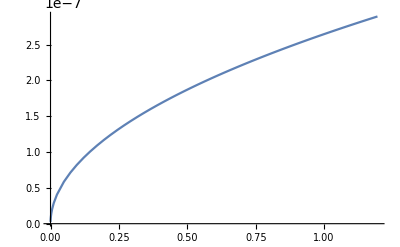

```mathematica
Plot[a2[t],{t,8.842938455704455*^-23, 1.1949916832033047*^-18},PlotRange->All]
```

```mathematica
ti*√k
```

8.84294×10^-23

```mathematica
√k*10^4
```

1.19499×10^-18

```mathematica
{E[√2(τi-P)]*ati^2 == Q^2*(1+E[2 √2(τi-P)]),√(2 ⅇ^(√2 (-P+τi))*(1+ⅇ^(2 √2 (-P+τi)))) *Daτi == (-1+ⅇ^(2 √2 (-P+τi))) *Q }, {P, Q}
```

```mathematica
Plot[a2[t],{t,8.84*10^(-23),1.1949916832033047*^-18},PlotRange->All]
```

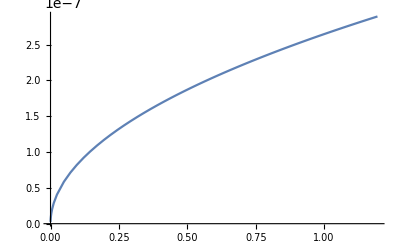
```mathematica
-Graphics-{E[√2(τi-P)]*ati^2 == Q^2*(1+E[2 √2(τi-P)]),√(2 ⅇ^(√2 (-P+τi))*(1+ⅇ^(2 √2 (-P+τi)))) *Daτi == (-1+ⅇ^(2 √2 (-P+τi))) *Q }, {P, Q}
```

```mathematica
n :=3
k = (4π *G)/(3*c^2)*ρ0 *(ati)^(3-n)
```

5.71202×10^-36

```mathematica
DSolve[a''[t]*a[t]+(a'[t])^2-(a[t])^2==0, a[t], t]
```

{{a[t]→ⅇ^(1/2 (-Log[ⅇ^(√2 (t-C[1]))]+Log[1+ⅇ^(2 √2 (t-C[1]))])) C[2]}}

```mathematica
FullSimplify[ⅇ^(1/2 (-Log[ⅇ^(√2 (t-C[1]))]+Log[1+ⅇ^(2 √2 (t-C[1]))])) C[2]]
```

(√(1+ⅇ^(2 √2 (t-C[1]))) C[2])/(√(ⅇ^(√2 (t-C[1]))))

```mathematica
a3[τ_]:= (Q √(1+ⅇ^(2 √2 (τ-P))))/(√(ⅇ^(√2 (τ-P))))
```

```mathematica
D[a3[τ], τ]
```

(√2 ⅇ^(2 √2 (-P+τ)) Q)/(√(ⅇ^(√2 (-P+τ))) √(1+ⅇ^(2 √2 (-P+τ))))-(√(1+ⅇ^(2 √2 (-P+τ))) Q)/(√2 √(ⅇ^(√2 (-P+τ))))

```mathematica
FullSimplify[(√2 ⅇ^(2 √2 (-P+τ)) Q)/(√(ⅇ^(√2 (-P+τ))) √(1+ⅇ^(2 √2 (-P+τ))))-(√(1+ⅇ^(2 √2 (-P+τ))) Q)/(√2 √(ⅇ^(√2 (-P+τ))))]
```

((-1+ⅇ^(2 √2 (-P+τ))) Q)/(√2 √(ⅇ^(√2 (-P+τ))) √(1+ⅇ^(2 √2 (-P+τ))))

```mathematica
NSolve[{E[√2(τi-P)]*ati^2 == Q^2*(1+E[2 √2(τi-P)]),√(2 ⅇ^(√2 (-P+τi))*(1+ⅇ^(2 √2 (-P+τi)))) *Daτi == (-1+ⅇ^(2 √2 (-P+τi))) *Q }, {P, Q}]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{}

```mathematica
Reduce[{E[√2(τi-P)]*ati^2 == Q^2*(1+E[2 √2(τi-P)]),√(2 ⅇ^(√2 (-P+τi))*(1+ⅇ^(2 √2 (-P+τi)))) *Daτi == (-1+ⅇ^(2 √2 (-P+τi))) *Q }, {P, Q}]
```

Reduce::inex: Reduce was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Reduce require exact input, providing Reduce with an exact version of the system may help.

Reduce[{6.25×10^-18 ⅇ[√2 (1.76859×10^-18-P)]==Q^2 (1+ⅇ[2 √2 (1.76859×10^-18-P)]),9.9114×10^8 √(ⅇ^(√2 (1.76859×10^-18-P)) (1+ⅇ^(2 √2 (1.76859×10^-18-P))))==(-1+ⅇ^(2 √2 (1.76859×10^-18-P))) Q},{P,Q}]

```mathematica
a3an[τ_] := √(R Cosh[√2 τ]+S Sinh[√2 τ])
```

```mathematica
D[a3an[τ], τ]
```

(√2 S Cosh[√2 τ]+√2 R Sinh[√2 τ])/(2 √(R Cosh[√2 τ]+S Sinh[√2 τ]))

```mathematica
NSolve[{ati^2 == R Cosh[√2 τi]+S Sinh[√2 τi], Daτi = (√2 S Cosh[√2 τi]+√2 R Sinh[√2 τi])/(2 √(R Cosh[√2 τi]+S Sinh[√2 τi]))}, {R, S}]
```

{{R→6.25×10^-18,S→0.}}

```mathematica
R:= 6.250000000000001*^-18
S := 0
```

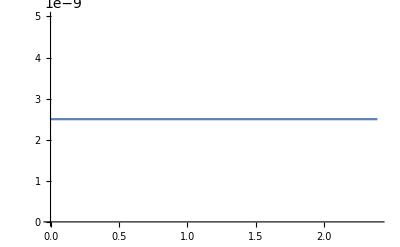

```mathematica
Plot[a3an[τ], {τ, τi, √k*10000}]
```

```mathematica
a3an[τ]
```

2.5×10^-9 √Cosh[√2 τ]